```mathematica
data=Import[NotebookDirectory[]<>"/test_format.tab"];
data2=Drop[data,1];
```

```mathematica
A=Transpose[{data2[[All,1]],data2[[All,2]]}];
B=Transpose[{data2[[All,1]]-0.0003,data2[[All,3]]}];
```

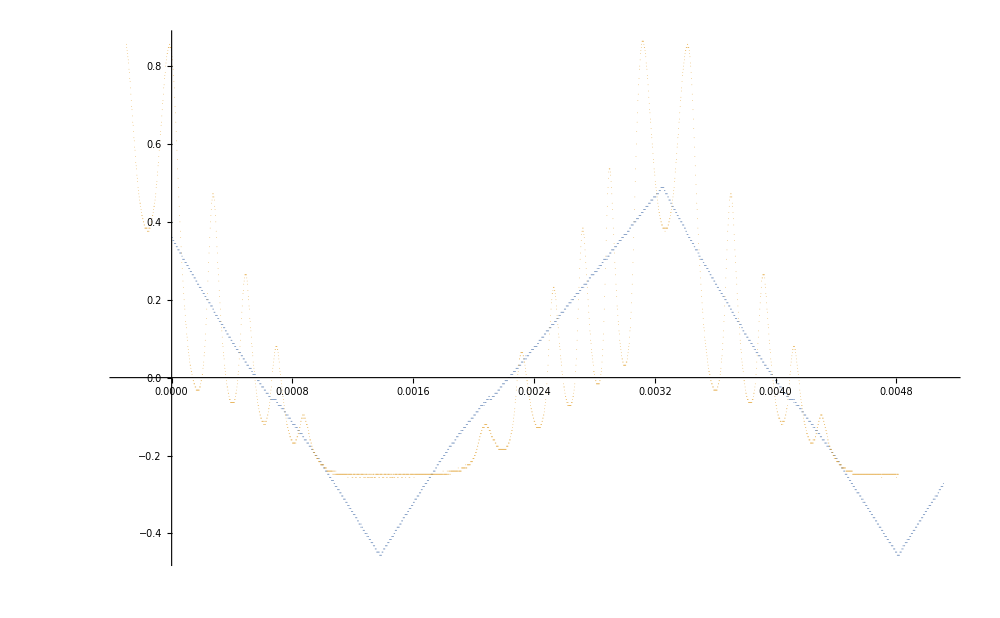

```mathematica
ListPlot[{A,B},ImageSize->1000, PlotStyle->{PointSize[0.0001]}]
```